```mathematica
SetDirectory["/Users/sashankkaushik/Documents/Sem III Acads/EP2110/Assignment"];
```

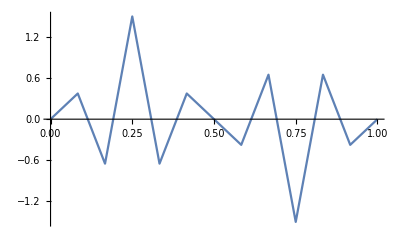

```mathematica
data12 = Import["data_12.dat"];
data21 = Import["data_21.dat"];
p1 = ListPlot[data12, Joined -> True]
```

```mathematica
L = 1;
N0 = 12;
```

```mathematica
x = Transpose[data12] [[1]];
fx = Transpose[data12][[2]];
cl1[l_] := Simplify[L/N0 Sum[fx[[i]]*Exp[-I((2π)/L)*l*x[[i]]], {i,12}]]
```

```mathematica
x1 = Range[-10,10];
y1 =Table[Abs[cl1[l]], {l,-10,10}]
ListPlot[Transpose[{x1,y1}]]
```

{3.78147×10^-16,0.125,5.17655×10^-16,0.5,5.56974×10^-16,0.5,2.50741×10^-16,0.125,1.14439×10^-16,0.125,2.498×10^-16,0.125,1.14439×10^-16,0.125,2.50741×10^-16,0.5,5.56974×10^-16,0.5,5.17655×10^-16,0.125,3.78147×10^-16}

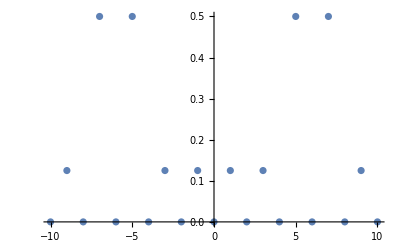

{-0.323685,1.5708,1.03114,-1.5708,-0.908911,1.5708,-0.521434,-1.5708,-2.89661,1.5708,π,-1.5708,2.89661,1.5708,0.521434,-1.5708,0.908911,1.5708,-1.03114,-1.5708,0.323685}

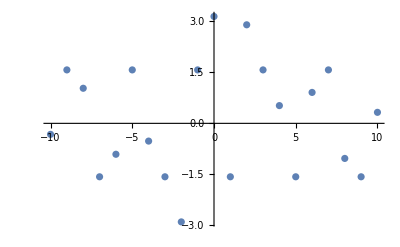

```mathematica
x2 = Range[-10,10];
y2 =Table[Arg[cl1[l]], {l,-10,10}]
ListPlot[Transpose[{x2,y2}]]
```

```mathematica
frec[x_] := Sum[cl1[l]*Exp[I*(2π)/L*l*x], {l, -10, 10}]
```

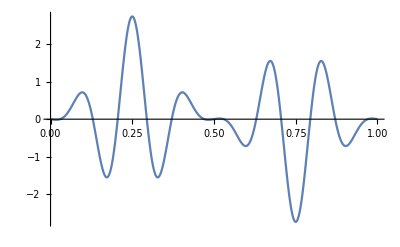

```mathematica
p2 = Plot[frec[t], {t, 0, 1}]
```

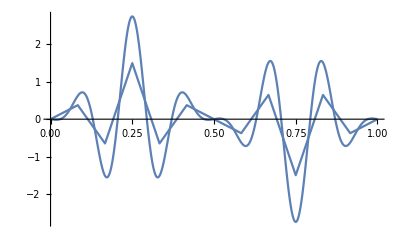

```mathematica
Show[p2, p1]
```

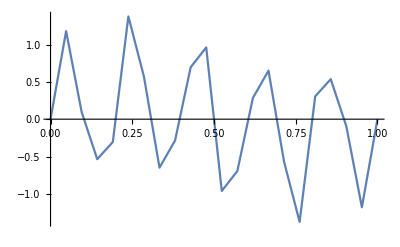

```mathematica
p3 = ListPlot[data21, Joined -> True]
```

```mathematica
L = 1;
N1 = 21;
```

```mathematica
x1 = Transpose[data21][[1]];
fx1 = Transpose[data21][[2]];
cl2[l_] := Simplify[L/N1 Sum[fx1[[i]]*Exp[-I((2π)/L)*l*x1[[i]]], {i,21}]]
```

{5.74443×10^-17,0.125,4.25117×10^-16,1.99501×10^-16,1.10391×10^-16,0.5,1.34605×10^-16,3.46354×10^-16,9.64746×10^-17,0.125,1.37456×10^-16,0.125,9.64746×10^-17,3.46354×10^-16,1.34605×10^-16,0.5,1.10391×10^-16,1.99501×10^-16,4.25117×10^-16,0.125,5.74443×10^-17}

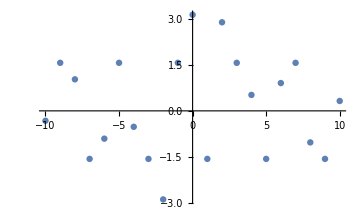

```mathematica
x3 = Range[-10,10];
y3 =Table[Abs[cl2[l]], {l,-10,10}]
ListPlot[Transpose[{x2,y2}]]
```

```mathematica
x4 = Range[-10,10];
y4 =Table[Arg[cl1[l]], {l,-10,10}]
ListPlot[Transpose[{x4,y4}]]
```

{-0.323685,1.5708,1.03114,-1.5708,-0.908911,1.5708,-0.521434,-1.5708,-2.89661,1.5708,π,-1.5708,2.89661,1.5708,0.521434,-1.5708,0.908911,1.5708,-1.03114,-1.5708,0.323685}

-Graphics-

```mathematica
frec1[x_] := Sum[cl2[l]*Exp[I*(2π)/L*l*x], {l, -10, 10}]
```

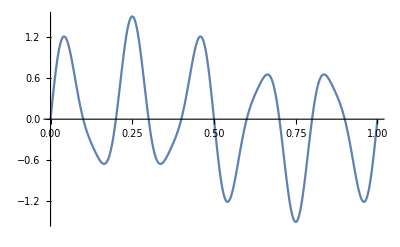

```mathematica
p4 = Plot[frec1[t], {t, 0, 1}]
```

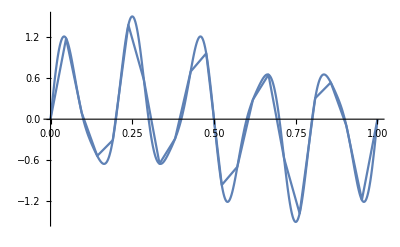

```mathematica
Show[p4,p3]
```